# Mobile Device Camera Calibration Using Building Images and Onboard Accelerometer

## Okay Arık and Seniha Esen Yuksel, Senior Member, IEEE

## Hacettepe University, Department of Electrical and Electronics Engineering, 06800, Beytepe, Ankara, Turkey

## okayarik@hacettepe.edu.tr, eyuksel@ee.hacettepe.edu.tr

## Abstract

Recent mobile devices are mostly integrated with camera and accelerometer sensors.As long as the device is immobile, the accelerometer is affected just by gravity, hence the measured acceleration refers to gravity.On the other hand, synchronized captured images can also carry the direction of gravity information depending on the content of the scene.For instance, structures as buildings, lighting poles, furniture, walls, etc.can show the direction of gravity on the images.These vertical structures in the image can be used to detect the vanishing point indicating zenith.Hence, estimation of the camera internal parameters which map gravity vector into the vanishing point is possible.Based on this theory, in this work, we propose a novel camera calibration method which only requires taking photos of an arbitrary building and recording the synchronous acceleration vectors from an onboard accelerometer.Then, the vanishing points detected from the images and the acceleration vectors replace the 3D calibrator.The resulting camera calibration method has competitive results compared to the popular calibrator - based methods despite it does not need any external calibrator object.The proposed camera calibration method both has the convenience of self - calibration approaches, and gives highly competitive accuracy within calibrator - based approaches.

## Calibration Application

The calibration application can be installed on an Android device using CamAcc.apk file. The application captures images and records the acceleration data synchronously. Take around 20 photos of a building by roughly rotating the device one turn around the principal axis of the camera. Images are saved inside CamAcc folder. Recorded acceleration data and corresponding image names are saved in acc.dat file in the same folder.

## Accelation Vectors

Computation of the bias of the accelerometer using records with 6 orientations (top, bottom, right, left, up, down) in abs.dat file

```mathematica
abs=Total[Partition[Map[#*UnitStep[Abs[#]-5000]&,Flatten[Take[Import[NotebookDirectory[]<>"abs.dat"],All,{2,4}]]],3]]/2.;
```

Index of the capture

```mathematica
cap=2; (* cap=0,1,...,15 *)
```

Import the accelerometer data, subtract the bias and normalize

```mathematica
acc=Take[Import[NotebookDirectory[]<>ExportString[cap,"Text"]<>"\\acc.dat"],All,{2,4}];
acv=Map[Normalize[#-abs]&,acc];
```

Number of images

```mathematica
is=Dimensions[acv][[1]];
```

## Detection of the Vetrical Lines and the Vanishing Point

List of the images

```mathematica
fls=Select[Import[NotebookDirectory[]<>ExportString[cap,"Text"]],StringContainsQ[#,"IMG"]&];
```

Number of images

```mathematica
is=Dimensions[fls][[1]];
```

Null matrix for vanishing points

```mathematica
sz=Table[0,{is},{2}];
```

Index of the image

```mathematica
in=1; (*in=1,2,...,is*)
```

Import the image

```mathematica
im=Import[NotebookDirectory[]<>ExportString[cap,"Text"]<>"\\"<>fls[[in]]];
```

Line detection using Hough method

```mathematica
ln=ImageLines[EdgeDetect[im,4]];
```

Select the vertical lines using acceleration vector

```mathematica
vt=Select[ln,Abs[Normalize[{1,-1}.#].({{0, -1}, {1, 0}}).Normalize[(Take[#,2]/N[#[[3]]])&[acv[[in]]]]]>.8&];
```

Visualize the selected vertical lines

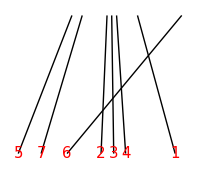

```mathematica
Graphics[{Map[Line,vt],
Table[Text[Style[n,15,Red],vt[[n,2]]],{n,1,Dimensions[vt][[1]]}]},ImageSize->200]
```

Drop the outlier lines, if any.

```mathematica
vt=Drop[vt,{6}];
```

Intersect the vertical lines and compute the vertical vanishing point

```mathematica
nr=Map[{1,-1}.#&,vt].({{0, -1}, {1, 0}});
na=Map[({1,-1}.#).({{0, -1}, {1, 0}}).#[[1]]&,vt];
szi=PseudoInverse[nr].na;
sz[[in]]=szi;
```

Save the computed vanishing points

```mathematica
If[Count[sz,0,2]==0,Export[NotebookDirectory[]<>ExportString[cap,"Text"]<>"\\sz.dat",sz]];
```

## Estimation of Projection Matrix

Projection Matrix P maps the unbiased acceleration vectors to the vertical vanishing points. (Eq. 6)

Import the vanishing points computed above

```mathematica
sz=Import[NotebookDirectory[]<>ExportString[cap,"Text"]<>"\\sz.dat"];
```

Transform the computed vanishing points to the coordinate system having the origin at the left-top corner.

```mathematica
sz=Map[{ImageDimensions[im][[2]]-#[[2]],#[[1]]}&,sz];
```

Get the spherical projection functions (SP1, SP2) and their Jacobians (JSP1, JSP2) for 3 distinct models: P~KR, P~KL and P~K

```mathematica
Get[NotebookDirectory[]<>"functions.wl"]
```

Optimization of the projection error function in Eq. 7 using Newton’s method for Model 3: P~K

Initialize:

```mathematica
k1 = 1/3000.; k2 = 0.; k3 = -1700*k1; k4 = 1/3000; k5 = -2300*k4;
```

Iterate:

```mathematica
For[n=1,n≤10,n=n+1,
dk=-PseudoInverse[Flatten[Table[JSP1[k1,k2,k3,k4,k5,sz[[n,1]],sz[[n,2]]],{n,is}],1]].Flatten[Table[SP1[k1,k2,k3,k4,k5,sz[[n,1]],sz[[n,2]]]+acv[[n]],{n,is}],1];
{k1,k2,k3,k4,k5}={k1,k2,k3,k4,k5}+dk;
]
```

Estimated Parameters for Model 3: P~K

```mathematica
Grid[{{"Focal Length",SpanFromLeft,"Principal Point",SpanFromLeft},{"horizontal","vertical","horizontal","vertical"},{#[[2,2]],#[[1,1]],#[[2,3]],#[[1,3]]}&[Inverse[({{k1, k2, k3}, {0, k4, k5}, {0, 0, 1}})]]},Frame->All]
```

Focal Length |  | Principal Point | 
horizontal | vertical | horizontal | vertical
3631.62 | 3646.57 | 2306.29 | 1750.19

Optimization of the projection error function in Eq. 7 using Newton's method for Model 1 & 2 : P~KR and P~KL

Initialize:

```mathematica
p11 = 1/3000.; p12 = 0.; p13 = -1700*p11; p21 = 0.; p22 = 1/3000.; p23 = -2300*p22; p31 = 0.; p32 = 0.;
```

Iterate:

```mathematica
For[n=1,n≤10,n=n+1,
dp=-PseudoInverse[Flatten[Table[JSP2[p11,p12,p13,p21,p22,p23,p31,p32,sz[[n,1]],sz[[n,2]]],{n,is}],1]].Flatten[Table[SP2[p11,p12,p13,p21,p22,p23,p31,p32,sz[[n,1]],sz[[n,2]]]+acv[[n]],{n,is}],1];
{p11,p12,p13,p21,p22,p23,p31,p32}={p11,p12,p13,p21,p22,p23,p31,p32}+dp;
]
```

Estimated Parameters for the Model 1: P~KR

```mathematica
Pe=Inverse[({{p11, p12, p13}, {p21, p22, p23}, {p31, p32, 1}})];
Grid[{{"Focal Length",SpanFromLeft,"Principal Point",SpanFromLeft},{"horizontal","vertical","horizontal","vertical"},{#[[2,2]],#[[1,1]],#[[2,3]],#[[1,3]]}&[#/#[[3,3]]&[CholeskyDecomposition[Transpose[Pe].Pe]]]},Frame->All]
```

Focal Length |  | Principal Point | 
horizontal | vertical | horizontal | vertical
3651.89 | 3670.15 | 2326.3 | 1753.14

Estimated Parameters for the Model 2 : P~KL

```mathematica
Pe=Inverse[({{p11, p12, p13}, {p21, p22, p23}, {p31, p32, 1}})];
```

```mathematica
Grid[{{"Focal Length",SpanFromLeft,"Principal Point",SpanFromLeft},{"horizontal","vertical","horizontal","vertical"},Abs[{#[[2,2]],#[[1,1]],#[[2,3]],#[[1,3]]}]&[#/#[[3,3]]&[Inverse[LUDecomposition[Inverse[Pe]][[1]]*{{1,1,1},{0,1,1},{0,0,1}}]]]},Frame->All]
```

Focal Length |  | Principal Point | 
horizontal | vertical | horizontal | vertical
3634.65 | 3642.61 | 2306.61 | 1759.45